```mathematica
SetDirectory["C:\\anaconda32\\Work\\Software\\Apps\\AutoPhaseCalib"]
```

C:\anaconda32\Work\Software\Apps\AutoPhaseCalib

```mathematica
data=.
(Print[#[[1]]];data[#[[1]]]=ToExpression[StringReplace[#[[2]],{"["->"{","]"->"}"}]])&/@Transpose[Import["linac1_approx_CrestingData.csv"]];
```

approxChargeData

approxPhaseFit

approxChargeFit

approxChargeStd

approxPhaseData

```mathematica
fitData=Select[Transpose[{data["approxPhaseData"],data["approxChargeData"]}],#[[2]]=!=20&]
```

{{83,-4.83179},{84,-1.94837},{85,-6.96787},{86,-5.98728},{87,-6.37277},{88,-11.8687},{89,-10.2476},{90,-8.98706},{91,-6.12932},{92,-3.01556},{93,-1.00915},{94,5.51635},{95,6.49011},{96,10.2521},{97,12.5069},{98,5.91716},{99,5.8211},{100,7.80311},{101,5.04504},{102,6.24866}}

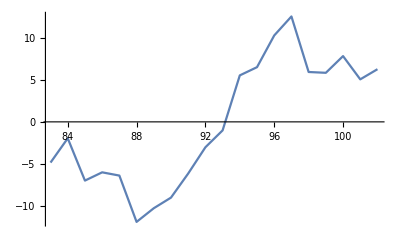

```mathematica
ListLinePlot[fitData]
```

```mathematica
Clear[crest]
```

```mathematica
fitans=FindFit[fitData,{eq = a+b Sin[c (x-crest)]},{a,{b,10}, c,{crest,92}},x]
```

{a→-0.0534514,b→9.61539,c→0.304518,crest→92.8753}

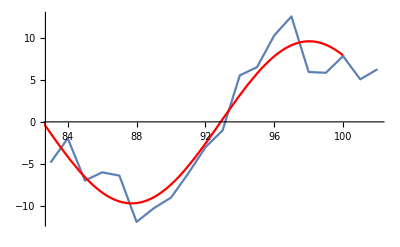

```mathematica
Show[ListLinePlot[fitData],
Plot[Evaluate[eq/.fitans],{x,70,100},PlotStyle->Red]]
```

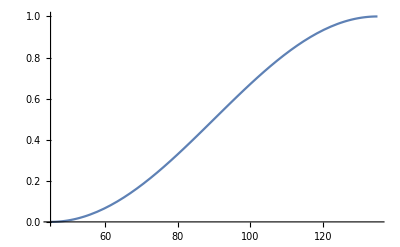

```mathematica
Plot[Cos[45 Degree+x Degree]^2,{x,45,135}]
```

```mathematica
Table[N@(Cos[45 Degree+x Degree]^2),{x,45,135}]
```

{0.,0.000304586,0.00121797,0.00273905,0.00486597,0.00759612,0.0109262,0.0148521,0.0193692,0.0244717,0.0301537,0.0364081,0.0432273,0.050603,0.0585262,0.0669873,0.075976,0.0854812,0.0954915,0.105995,0.116978,0.128428,0.14033,0.152671,0.165435,0.178606,0.192169,0.206107,0.220404,0.23504,0.25,0.265264,0.280814,0.296632,0.312697,0.32899,0.345492,0.362181,0.379039,0.396044,0.413176,0.430413,0.447736,0.465122,0.48255,0.5,0.51745,0.534878,0.552264,0.569587,0.586824,0.603956,0.620961,0.637819,0.654508,0.67101,0.687303,0.703368,0.719186,0.734736,0.75,0.76496,0.779596,0.793893,0.807831,0.821394,0.834565,0.847329,0.85967,0.871572,0.883022,0.894005,0.904508,0.914519,0.924024,0.933013,0.941474,0.949397,0.956773,0.963592,0.969846,0.975528,0.980631,0.985148,0.989074,0.992404,0.995134,0.997261,0.998782,0.999695,1.}